```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,4000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

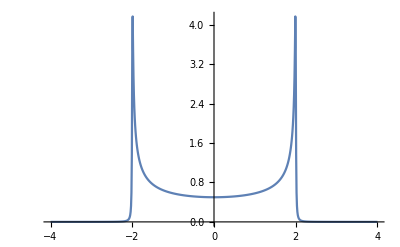

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0][[1,1]]]},{ω,Range[-4,4,0.01]}],PlotRange->All]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:= Inverse[(ω+ⅈ*δ-ϵ1)IdentityMatrix[1]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_,n_,o_,p_,q_,r_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1],imp=imp[ω,δ,t,ϵ,ϵ1]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,n]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,m]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,o]; J=J];(*sl6=Inverse[IdentityMatrix[1]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[1]-imp.T.sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,q]; J=J];sl9=Inverse[IdentityMatrix[1]-imp.T.sl8.T].imp; sl10=Module[{J=sl9},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,r]; J=J];*)Il1:=Inverse[IdentityMatrix[1]-sl5.T1[1].SR[ω,0.001,1,0].T1[1]].sl5;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T1[1].sl5.T1[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
RandomInteger[{0,16}]
```

7

```mathematica
Mean[Table[tr1[0.1,0.01,1,0,1,RandomInteger[{0,40}],RandomInteger[{0,40}],RandomInteger[{0,16}],RandomInteger[{0,16}],RandomInteger[{0,16}],RandomInteger[{0,16}]],10000]]
```

0.756297

```mathematica
f[ϵ1_]:=Table[{ω,Mean[Table[tr1[ω,0.01,1,0,ϵ1,RandomInteger[{0,40}],RandomInteger[{0,40}],RandomInteger[{0,16}],RandomInteger[{0,16}],RandomInteger[{0,16}],RandomInteger[{0,16}]],10000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
Export["1d2imp1.csv",f[1]]
```

1d2imp1.csv

```mathematica
Export["1d2imp3.csv",f[0.3]]
```

1d2imp3.csv

```mathematica
Export["1d2imp4.csv",f[0.4]]
```

1d2imp4.csv

```mathematica
Export["1d2imp5.csv",f[0.5]]
```

1d2imp5.csv

```mathematica
Export["1d2imp6.csv",f[0.6]]
```

1d2imp6.csv

```mathematica
Export["1d2imp7.csv",f[0.7]]
```

1d2imp7.csv

```mathematica
Export["1d2imp8.csv",f[0.8]]
```

1d2imp8.csv

```mathematica
Export["1d2imp9.csv",f[9]]
```

1d2imp9.csv

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:= Inverse[(ω+ⅈ*δ-ϵ1)IdentityMatrix[1]]
```

```mathematica
sl6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{m=RandomInteger[{0,20}],n=RandomInteger[{0,20}],o=RandomInteger[{0,20}],gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1],imp=imp[ω,δ,t,ϵ,ϵ1]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,m]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,n]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,o]; J=J]]
```

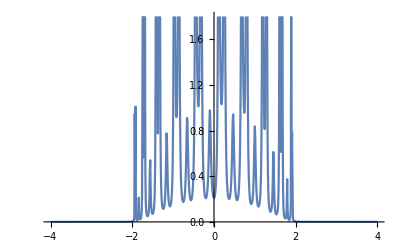

```mathematica
ListLinePlot[Table[{ω,-Im[sl6[ω,0.001,1,0,1][[1,1]]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
sl7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1],imp=imp[ω,δ,t,ϵ,ϵ1],m=RandomInteger[{0,20}],n=RandomInteger[{0,20}],o=RandomInteger[{0,20}]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,m]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,n]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,o]; J=J]]
```

```mathematica
Table[{ω,Mean[Table[sl7[ω,0.001,1,0,0.7],10000]]},{ω,Range[-3,3,0.01]}]
```

{{-3.,{{-0.377339-0.000166421 ⅈ}}},{-2.99,{{-0.378931-0.000168096 ⅈ}}},{-2.98,{{-0.3809-0.000170129 ⅈ}}},{-2.97,{{-0.382371-0.000171711 ⅈ}}},{-2.96,{{-0.3843-0.000173726 ⅈ}}},{-2.95,{{-0.386228-0.000175748 ⅈ}}},{-2.94,{{-0.387931-0.000177624 ⅈ}}},{-2.93,{{-0.389568-0.000179364 ⅈ}}},{-2.92,{{-0.391297-0.000181225 ⅈ}}},{-2.91,{{-0.393155-0.000183295 ⅈ}}},{-2.9,{{-0.394482-0.000184931 ⅈ}}},{-2.89,{{-0.396635-0.000187267 ⅈ}}},{-2.88,{{-0.398674-0.000189477 ⅈ}}},{-2.87,{{-0.400505-0.00019168 ⅈ}}},{-2.86,{{-0.402567-0.00019396 ⅈ}}},{-2.85,{{-0.404343-0.000196041 ⅈ}}},{-2.84,{{-0.406261-0.000198324 ⅈ}}},{-2.83,{{-0.408663-0.000201022 ⅈ}}},{-2.82,{{-0.410301-0.000203081 ⅈ}}},{-2.81,{{-0.412549-0.000205686 ⅈ}}},{-2.8,{{-0.415254-0.00020881 ⅈ}}},{-2.79,{{-0.416759-0.000210794 ⅈ}}},{-2.78,{{-0.418816-0.000213414 ⅈ}}},{-2.77,{{-0.420796-0.000215955 ⅈ}}},{-2.76,{{-0.423373-0.000219077 ⅈ}}},{-2.75,{{-0.425654-0.000221913 ⅈ}}},{-2.74,{{-0.428094-0.000224984 ⅈ}}},{-2.73,{{-0.430123-0.000227763 ⅈ}}},{-2.72,{{-0.432398-0.000230631 ⅈ}}},{-2.71,{{-0.434505-0.000233479 ⅈ}}},{-2.7,{{-0.436996-0.000236829 ⅈ}}},{-2.69,{{-0.438819-0.00023951 ⅈ}}},{-2.68,{{-0.441772-0.00024332 ⅈ}}},{-2.67,{{-0.444192-0.000246603 ⅈ}}},{-2.66,{{-0.446897-0.000250468 ⅈ}}},{-2.65,{{-0.448846-0.00025334 ⅈ}}},{-2.64,{{-0.451781-0.000257422 ⅈ}}},{-2.63,{{-0.454392-0.000261188 ⅈ}}},{-2.62,{{-0.456725-0.000264726 ⅈ}}},{-2.61,{{-0.459709-0.000268968 ⅈ}}},{-2.6,{{-0.462477-0.000273061 ⅈ}}},{-2.59,{{-0.464952-0.000276855 ⅈ}}},{-2.58,{{-0.467735-0.000281104 ⅈ}}},{-2.57,{{-0.470729-0.000285973 ⅈ}}},{-2.56,{{-0.473743-0.000290435 ⅈ}}},{-2.55,{{-0.476352-0.000294775 ⅈ}}},{-2.54,{{-0.479441-0.000299703 ⅈ}}},{-2.53,{{-0.482992-0.000305362 ⅈ}}},{-2.52,{{-0.485277-0.000309642 ⅈ}}},{-2.51,{{-0.489195-0.000315766 ⅈ}}},{-2.5,{{-0.492224-0.00032105 ⅈ}}},{-2.49,{{-0.49515-0.000326401 ⅈ}}},{-2.48,{{-0.498112-0.000331657 ⅈ}}},{-2.47,{{-0.501888-0.000338329 ⅈ}}},{-2.46,{{-0.505225-0.000344524 ⅈ}}},{-2.45,{{-0.508932-0.000351187 ⅈ}}},{-2.44,{{-0.512344-0.000357563 ⅈ}}},{-2.43,{{-0.515956-0.000364556 ⅈ}}},{-2.42,{{-0.519281-0.000371369 ⅈ}}},{-2.41,{{-0.523291-0.000379545 ⅈ}}},{-2.4,{{-0.527099-0.00038672 ⅈ}}},{-2.39,{{-0.531028-0.000394929 ⅈ}}},{-2.38,{{-0.535073-0.000403258 ⅈ}}},{-2.37,{{-0.538947-0.000411866 ⅈ}}},{-2.36,{{-0.54322-0.000421205 ⅈ}}},{-2.35,{{-0.547104-0.000430227 ⅈ}}},{-2.34,{{-0.552382-0.000441459 ⅈ}}},{-2.33,{{-0.556126-0.000450865 ⅈ}}},{-2.32,{{-0.56062-0.000461849 ⅈ}}},{-2.31,{{-0.565561-0.000473818 ⅈ}}},{-2.3,{{-0.57089-0.000486165 ⅈ}}},{-2.29,{{-0.575637-0.000499448 ⅈ}}},{-2.28,{{-0.58005-0.000510829 ⅈ}}},{-2.27,{{-0.584679-0.000524404 ⅈ}}},{-2.26,{{-0.590159-0.000540027 ⅈ}}},{-2.25,{{-0.59664-0.000557071 ⅈ}}},{-2.24,{{-0.601768-0.000573315 ⅈ}}},{-2.23,{{-0.607722-0.000590894 ⅈ}}},{-2.22,{{-0.61353-0.000609617 ⅈ}}},{-2.21,{{-0.620707-0.00063206 ⅈ}}},{-2.2,{{-0.625984-0.000651682 ⅈ}}},{-2.19,{{-0.632742-0.000675676 ⅈ}}},{-2.18,{{-0.640833-0.000703931 ⅈ}}},{-2.17,{{-0.646578-0.000728482 ⅈ}}},{-2.16,{{-0.654954-0.000759601 ⅈ}}},{-2.15,{{-0.662916-0.000793449 ⅈ}}},{-2.14,{{-0.670153-0.000828117 ⅈ}}},{-2.13,{{-0.678872-0.000868712 ⅈ}}},{-2.12,{{-0.688567-0.000915408 ⅈ}}},{-2.11,{{-0.695584-0.000959734 ⅈ}}},{-2.1,{{-0.707336-0.0010217 ⅈ}}},{-2.09,{{-0.717325-0.00108416 ⅈ}}},{-2.08,{{-0.726988-0.00115422 ⅈ}}},{-2.07,{{-0.741463-0.00125366 ⅈ}}},{-2.06,{{-0.753493-0.00135755 ⅈ}}},{-2.05,{{-0.767887-0.00148954 ⅈ}}},{-2.04,{{-0.785043-0.00166813 ⅈ}}},{-2.03,{{-0.800472-0.00187895 ⅈ}}},{-2.02,{{-0.822336-0.00222025 ⅈ}}},{-2.01,{{-0.84559-0.00272835 ⅈ}}},{-2.,{{-0.878072-0.00376627 ⅈ}}},{-1.99,{{-0.925756-0.00708529 ⅈ}}},{-1.98,{{-1.01669-0.11045 ⅈ}}},{-1.97,{{-0.939801-0.153879 ⅈ}}},{-1.96,{{-0.943697-0.130457 ⅈ}}},{-1.95,{{-0.913444-0.153241 ⅈ}}},{-1.94,{{-0.935157-0.144266 ⅈ}}},{-1.93,{{-0.983679-0.178199 ⅈ}}},{-1.92,{{-0.978076-0.296872 ⅈ}}},{-1.91,{{-0.944538-0.300936 ⅈ}}},{-1.9,{{-0.908642-0.300661 ⅈ}}},{-1.89,{{-0.926741-0.296479 ⅈ}}},{-1.88,{{-0.912285-0.332117 ⅈ}}},{-1.87,{{-0.907229-0.299912 ⅈ}}},{-1.86,{{-0.92309-0.301482 ⅈ}}},{-1.85,{{-0.937118-0.365915 ⅈ}}},{-1.84,{{-0.924332-0.319993 ⅈ}}},{-1.83,{{-0.978896-0.363745 ⅈ}}},{-1.82,{{-0.928143-0.406788 ⅈ}}},{-1.81,{{-0.927835-0.405013 ⅈ}}},{-1.8,{{-0.897842-0.469722 ⅈ}}},{-1.79,{{-0.882251-0.418413 ⅈ}}},{-1.78,{{-0.878326-0.455637 ⅈ}}},{-1.77,{{-0.881435-0.443781 ⅈ}}},{-1.76,{{-0.861102-0.430334 ⅈ}}},{-1.75,{{-0.881933-0.438518 ⅈ}}},{-1.74,{{-0.888334-0.444496 ⅈ}}},{-1.73,{{-0.881601-0.496723 ⅈ}}},{-1.72,{{-0.838299-0.473201 ⅈ}}},{-1.71,{{-0.868251-0.467469 ⅈ}}},{-1.7,{{-0.877662-0.476055 ⅈ}}},{-1.69,{{-0.885577-0.519275 ⅈ}}},{-1.68,{{-0.86688-0.550169 ⅈ}}},{-1.67,{{-0.863274-0.551329 ⅈ}}},{-1.66,{{-0.826285-0.553119 ⅈ}}},{-1.65,{{-0.818245-0.551658 ⅈ}}},{-1.64,{{-0.823797-0.561279 ⅈ}}},{-1.63,{{-0.827033-0.537713 ⅈ}}},{-1.62,{{-0.852719-0.571709 ⅈ}}},{-1.61,{{-0.787532-0.630257 ⅈ}}},{-1.6,{{-0.766736-0.588002 ⅈ}}},{-1.59,{{-0.766309-0.555561 ⅈ}}},{-1.58,{{-0.788674-0.573865 ⅈ}}},{-1.57,{{-0.768701-0.592421 ⅈ}}},{-1.56,{{-0.775479-0.610978 ⅈ}}},{-1.55,{{-0.784219-0.589965 ⅈ}}},{-1.54,{{-0.790711-0.592014 ⅈ}}},{-1.53,{{-0.810959-0.630468 ⅈ}}},{-1.52,{{-0.7974-0.633355 ⅈ}}},{-1.51,{{-0.800203-0.650091 ⅈ}}},{-1.5,{{-0.770248-0.666571 ⅈ}}},{-1.49,{{-0.736218-0.671086 ⅈ}}},{-1.48,{{-0.738858-0.660637 ⅈ}}},{-1.47,{{-0.743198-0.676292 ⅈ}}},{-1.46,{{-0.71994-0.689115 ⅈ}}},{-1.45,{{-0.696147-0.675825 ⅈ}}},{-1.44,{{-0.695706-0.656138 ⅈ}}},{-1.43,{{-0.715525-0.630962 ⅈ}}},{-1.42,{{-0.765625-0.63271 ⅈ}}},{-1.41,{{-0.783621-0.716725 ⅈ}}},{-1.4,{{-0.72009-0.73612 ⅈ}}},{-1.39,{{-0.698143-0.740603 ⅈ}}},{-1.38,{{-0.671911-0.72156 ⅈ}}},{-1.37,{{-0.678188-0.70172 ⅈ}}},{-1.36,{{-0.692133-0.693432 ⅈ}}},{-1.35,{{-0.6928-0.710953 ⅈ}}},{-1.34,{{-0.692976-0.716432 ⅈ}}},{-1.33,{{-0.696181-0.728057 ⅈ}}},{-1.32,{{-0.683332-0.733561 ⅈ}}},{-1.31,{{-0.680743-0.760757 ⅈ}}},{-1.3,{{-0.676087-0.770304 ⅈ}}},{-1.29,{{-0.651043-0.766439 ⅈ}}},{-1.28,{{-0.649647-0.78248 ⅈ}}},{-1.27,{{-0.628392-0.781198 ⅈ}}},{-1.26,{{-0.629519-0.784236 ⅈ}}},{-1.25,{{-0.629342-0.775222 ⅈ}}},{-1.24,{{-0.614548-0.792307 ⅈ}}},{-1.23,{{-0.602956-0.776721 ⅈ}}},{-1.22,{{-0.580888-0.793918 ⅈ}}},{-1.21,{{-0.581664-0.776581 ⅈ}}},{-1.2,{{-0.584644-0.778398 ⅈ}}},{-1.19,{{-0.577619-0.776601 ⅈ}}},{-1.18,{{-0.585564-0.782811 ⅈ}}},{-1.17,{{-0.58035-0.778781 ⅈ}}},{-1.16,{{-0.58169-0.797389 ⅈ}}},{-1.15,{{-0.578922-0.793602 ⅈ}}},{-1.14,{{-0.575126-0.802474 ⅈ}}},{-1.13,{{-0.569115-0.797834 ⅈ}}},{-1.12,{{-0.572613-0.787991 ⅈ}}},{-1.11,{{-0.564065-0.800601 ⅈ}}},{-1.1,{{-0.588896-0.805203 ⅈ}}},{-1.09,{{-0.577147-0.829748 ⅈ}}},{-1.08,{{-0.565821-0.843733 ⅈ}}},{-1.07,{{-0.552585-0.851723 ⅈ}}},{-1.06,{{-0.525879-0.871201 ⅈ}}},{-1.05,{{-0.497346-0.857627 ⅈ}}},{-1.04,{{-0.490264-0.839472 ⅈ}}},{-1.03,{{-0.472903-0.822643 ⅈ}}},{-1.02,{{-0.476182-0.78533 ⅈ}}},{-1.01,{{-0.521502-0.762704 ⅈ}}},{-1.,{{-0.553296-0.791562 ⅈ}}},{-0.99,{{-0.563646-0.837155 ⅈ}}},{-0.98,{{-0.559452-0.85198 ⅈ}}},{-0.97,{{-0.545866-0.872069 ⅈ}}},{-0.96,{{-0.544461-0.896097 ⅈ}}},{-0.95,{{-0.498172-0.919063 ⅈ}}},{-0.94,{{-0.483302-0.908351 ⅈ}}},{-0.93,{{-0.472527-0.886379 ⅈ}}},{-0.92,{{-0.461569-0.896087 ⅈ}}},{-0.91,{{-0.458662-0.861907 ⅈ}}},{-0.9,{{-0.466943-0.880469 ⅈ}}},{-0.89,{{-0.462232-0.874306 ⅈ}}},{-0.88,{{-0.478386-0.871557 ⅈ}}},{-0.87,{{-0.481782-0.893977 ⅈ}}},{-0.86,{{-0.474066-0.904131 ⅈ}}},{-0.85,{{-0.47151-0.902821 ⅈ}}},{-0.84,{{-0.454511-0.90536 ⅈ}}},{-0.83,{{-0.44387-0.913068 ⅈ}}},{-0.82,{{-0.443135-0.915372 ⅈ}}},{-0.81,{{-0.445629-0.92425 ⅈ}}},{-0.8,{{-0.419977-0.929233 ⅈ}}},{-0.79,{{-0.40873-0.932316 ⅈ}}},{-0.78,{{-0.417764-0.935202 ⅈ}}},{-0.77,{{-0.401534-0.92898 ⅈ}}},{-0.76,{{-0.387205-0.945868 ⅈ}}},{-0.75,{{-0.39456-0.945894 ⅈ}}},{-0.74,{{-0.362313-0.929158 ⅈ}}},{-0.73,{{-0.368216-0.933608 ⅈ}}},{-0.72,{{-0.373796-0.921232 ⅈ}}},{-0.71,{{-0.361273-0.92997 ⅈ}}},{-0.7,{{-0.360673-0.942925 ⅈ}}},{-0.69,{{-0.355221-0.936708 ⅈ}}},{-0.68,{{-0.32248-0.936667 ⅈ}}},{-0.67,{{-0.330753-0.931364 ⅈ}}},{-0.66,{{-0.322118-0.939761 ⅈ}}},{-0.65,{{-0.31174-0.926887 ⅈ}}},{-0.64,{{-0.330389-0.945566 ⅈ}}},{-0.63,{{-0.324171-0.930988 ⅈ}}},{-0.62,{{-0.325673-0.935953 ⅈ}}},{-0.61,{{-0.322247-0.942896 ⅈ}}},{-0.6,{{-0.313659-0.945536 ⅈ}}},{-0.59,{{-0.309086-0.937001 ⅈ}}},{-0.58,{{-0.32051-0.952696 ⅈ}}},{-0.57,{{-0.31043-0.94567 ⅈ}}},{-0.56,{{-0.30549-0.971429 ⅈ}}},{-0.55,{{-0.300105-0.969332 ⅈ}}},{-0.54,{{-0.299291-0.969718 ⅈ}}},{-0.53,{{-0.286746-0.972204 ⅈ}}},{-0.52,{{-0.274743-0.985918 ⅈ}}},{-0.51,{{-0.251165-0.986541 ⅈ}}},{-0.5,{{-0.261826-0.980997 ⅈ}}},{-0.49,{{-0.244277-0.987721 ⅈ}}},{-0.48,{{-0.237073-0.984113 ⅈ}}},{-0.47,{{-0.228813-0.993832 ⅈ}}},{-0.46,{{-0.212295-0.973229 ⅈ}}},{-0.45,{{-0.222983-0.968101 ⅈ}}},{-0.44,{{-0.211895-0.979037 ⅈ}}},{-0.43,{{-0.224603-0.974643 ⅈ}}},{-0.42,{{-0.212756-0.97916 ⅈ}}},{-0.41,{{-0.207746-0.98302 ⅈ}}},{-0.4,{{-0.204131-0.991257 ⅈ}}},{-0.39,{{-0.186659-0.98229 ⅈ}}},{-0.38,{{-0.184791-0.99648 ⅈ}}},{-0.37,{{-0.157487-0.984246 ⅈ}}},{-0.36,{{-0.162435-0.987317 ⅈ}}},{-0.35,{{-0.163751-0.97225 ⅈ}}},{-0.34,{{-0.175288-0.967514 ⅈ}}},{-0.33,{{-0.165932-0.959075 ⅈ}}},{-0.32,{{-0.173731-0.970995 ⅈ}}},{-0.31,{{-0.171745-0.95755 ⅈ}}},{-0.3,{{-0.165515-0.981086 ⅈ}}},{-0.29,{{-0.176643-0.98106 ⅈ}}},{-0.28,{{-0.163867-0.993775 ⅈ}}},{-0.27,{{-0.166069-1.00966 ⅈ}}},{-0.26,{{-0.150069-1.01604 ⅈ}}},{-0.25,{{-0.151181-1.02562 ⅈ}}},{-0.24,{{-0.138275-1.02389 ⅈ}}},{-0.23,{{-0.129985-1.01764 ⅈ}}},{-0.22,{{-0.107293-1.0301 ⅈ}}},{-0.21,{{-0.0913573-1.01493 ⅈ}}},{-0.2,{{-0.077137-1.02797 ⅈ}}},{-0.19,{{-0.0706281-1.00452 ⅈ}}},{-0.18,{{-0.0597517-1.00165 ⅈ}}},{-0.17,{{-0.058536-0.989509 ⅈ}}},{-0.16,{{-0.0677376-0.98324 ⅈ}}},{-0.15,{{-0.0703268-1.00176 ⅈ}}},{-0.14,{{-0.0732605-1.00491 ⅈ}}},{-0.13,{{-0.0667357-1.01654 ⅈ}}},{-0.12,{{-0.0671865-1.02597 ⅈ}}},{-0.11,{{-0.0514566-1.04068 ⅈ}}},{-0.1,{{-0.0334909-1.03446 ⅈ}}},{-0.09,{{0.0055085-1.05868 ⅈ}}},{-0.08,{{0.0176567-1.04201 ⅈ}}},{-0.07,{{0.0209495-1.03394 ⅈ}}},{-0.06,{{0.0303605-1.05236 ⅈ}}},{-0.05,{{0.0806406-1.07156 ⅈ}}},{-0.04,{{0.12727-1.04166 ⅈ}}},{-0.03,{{0.17638-1.00513 ⅈ}}},{-0.02,{{0.183752-0.933024 ⅈ}}},{-0.01,{{0.155833-0.866774 ⅈ}}},{0.,{{0.131775-0.846885 ⅈ}}},{0.01,{{0.101626-0.82965 ⅈ}}},{0.02,{{0.0719078-0.798336 ⅈ}}},{0.03,{{0.0308419-0.78851 ⅈ}}},{0.04,{{-0.0130359-0.788841 ⅈ}}},{0.05,{{-0.0492685-0.806487 ⅈ}}},{0.06,{{-0.0987393-0.828153 ⅈ}}},{0.07,{{-0.136038-0.895646 ⅈ}}},{0.08,{{-0.132993-0.959548 ⅈ}}},{0.09,{{-0.0916826-1.00504 ⅈ}}},{0.1,{{-0.0486378-1.03025 ⅈ}}},{0.11,{{0.00100224-1.02843 ⅈ}}},{0.12,{{0.0178235-1.01425 ⅈ}}},{0.13,{{0.0543241-1.01329 ⅈ}}},{0.14,{{0.0636429-1.0114 ⅈ}}},{0.15,{{0.0804718-1.01059 ⅈ}}},{0.16,{{0.0861088-0.97513 ⅈ}}},{0.17,{{0.0753167-0.958401 ⅈ}}},{0.18,{{0.0889042-0.958704 ⅈ}}},{0.19,{{0.0890842-0.95238 ⅈ}}},{0.2,{{0.0719402-0.935893 ⅈ}}},{0.21,{{0.0698566-0.943491 ⅈ}}},{0.22,{{0.048352-0.952839 ⅈ}}},{0.23,{{0.0578901-0.974914 ⅈ}}},{0.24,{{0.0637075-0.96896 ⅈ}}},{0.25,{{0.0769761-0.98083 ⅈ}}},{0.26,{{0.0700924-0.99926 ⅈ}}},{0.27,{{0.0869802-0.984206 ⅈ}}},{0.28,{{0.102356-0.97865 ⅈ}}},{0.29,{{0.112631-0.981921 ⅈ}}},{0.3,{{0.118684-0.981686 ⅈ}}},{0.31,{{0.124526-0.97031 ⅈ}}},{0.32,{{0.126949-0.974971 ⅈ}}},{0.33,{{0.140768-0.956188 ⅈ}}},{0.34,{{0.138855-0.974894 ⅈ}}},{0.35,{{0.145019-0.986647 ⅈ}}},{0.36,{{0.139813-0.974425 ⅈ}}},{0.37,{{0.144486-0.979668 ⅈ}}},{0.38,{{0.137806-0.993263 ⅈ}}},{0.39,{{0.151969-0.991513 ⅈ}}},{0.4,{{0.187485-0.997669 ⅈ}}},{0.41,{{0.19421-0.993495 ⅈ}}},{0.42,{{0.198551-1.00461 ⅈ}}},{0.43,{{0.21132-0.98392 ⅈ}}},{0.44,{{0.205841-0.982921 ⅈ}}},{0.45,{{0.225417-0.965848 ⅈ}}},{0.46,{{0.227756-0.962861 ⅈ}}},{0.47,{{0.231775-0.940526 ⅈ}}},{0.48,{{0.235278-0.951157 ⅈ}}},{0.49,{{0.233948-0.936639 ⅈ}}},{0.5,{{0.226883-0.948695 ⅈ}}},{0.51,{{0.228858-0.931592 ⅈ}}},{0.52,{{0.222222-0.949294 ⅈ}}},{0.53,{{0.221884-0.955132 ⅈ}}},{0.54,{{0.230125-0.953275 ⅈ}}},{0.55,{{0.228304-0.960223 ⅈ}}},{0.56,{{0.231687-0.976657 ⅈ}}},{0.57,{{0.257512-0.96444 ⅈ}}},{0.58,{{0.263296-0.954014 ⅈ}}},{0.59,{{0.256339-0.946051 ⅈ}}},{0.6,{{0.261887-0.949883 ⅈ}}},{0.61,{{0.276957-0.952702 ⅈ}}},{0.62,{{0.283624-0.955652 ⅈ}}},{0.63,{{0.284639-0.967833 ⅈ}}},{0.64,{{0.283743-0.959907 ⅈ}}},{0.65,{{0.296626-0.952453 ⅈ}}},{0.66,{{0.314616-0.95584 ⅈ}}},{0.67,{{0.305492-0.949155 ⅈ}}},{0.68,{{0.326912-0.95171 ⅈ}}},{0.69,{{0.323358-0.954916 ⅈ}}},{0.7,{{0.360821-0.943528 ⅈ}}},{0.71,{{0.363397-0.932654 ⅈ}}},{0.72,{{0.3594-0.942763 ⅈ}}},{0.73,{{0.363189-0.929047 ⅈ}}},{0.74,{{0.368019-0.942104 ⅈ}}},{0.75,{{0.359042-0.912405 ⅈ}}},{0.76,{{0.371586-0.903705 ⅈ}}},{0.77,{{0.382728-0.896111 ⅈ}}},{0.78,{{0.364923-0.897127 ⅈ}}},{0.79,{{0.388518-0.895755 ⅈ}}},{0.8,{{0.365528-0.898063 ⅈ}}},{0.81,{{0.383807-0.903147 ⅈ}}},{0.82,{{0.377799-0.909264 ⅈ}}},{0.83,{{0.386376-0.908171 ⅈ}}},{0.84,{{0.392907-0.914892 ⅈ}}},{0.85,{{0.40722-0.910455 ⅈ}}},{0.86,{{0.426413-0.898684 ⅈ}}},{0.87,{{0.423261-0.892188 ⅈ}}},{0.88,{{0.419271-0.890742 ⅈ}}},{0.89,{{0.414687-0.893143 ⅈ}}},{0.9,{{0.414738-0.891926 ⅈ}}},{0.91,{{0.436031-0.900628 ⅈ}}},{0.92,{{0.426272-0.921715 ⅈ}}},{0.93,{{0.447499-0.914497 ⅈ}}},{0.94,{{0.468101-0.92186 ⅈ}}},{0.95,{{0.49895-0.886327 ⅈ}}},{0.96,{{0.513389-0.874808 ⅈ}}},{0.97,{{0.521311-0.84691 ⅈ}}},{0.98,{{0.526535-0.805366 ⅈ}}},{0.99,{{0.474167-0.777033 ⅈ}}},{1.,{{0.439026-0.787168 ⅈ}}},{1.01,{{0.440249-0.815056 ⅈ}}},{1.02,{{0.44295-0.825339 ⅈ}}},{1.03,{{0.445068-0.833427 ⅈ}}},{1.04,{{0.445429-0.851133 ⅈ}}},{1.05,{{0.47471-0.871767 ⅈ}}},{1.06,{{0.503725-0.87292 ⅈ}}},{1.07,{{0.482553-0.846056 ⅈ}}},{1.08,{{0.511176-0.852849 ⅈ}}},{1.09,{{0.51957-0.827188 ⅈ}}},{1.1,{{0.509451-0.834259 ⅈ}}},{1.11,{{0.500675-0.831383 ⅈ}}},{1.12,{{0.511157-0.835482 ⅈ}}},{1.13,{{0.518443-0.84497 ⅈ}}},{1.14,{{0.526027-0.84394 ⅈ}}},{1.15,{{0.550297-0.838437 ⅈ}}},{1.16,{{0.548694-0.824527 ⅈ}}},{1.17,{{0.559028-0.809967 ⅈ}}},{1.18,{{0.564167-0.820568 ⅈ}}},{1.19,{{0.57416-0.820135 ⅈ}}},{1.2,{{0.571386-0.826715 ⅈ}}},{1.21,{{0.584916-0.842355 ⅈ}}},{1.22,{{0.599343-0.823956 ⅈ}}},{1.23,{{0.614456-0.807871 ⅈ}}},{1.24,{{0.62296-0.790694 ⅈ}}},{1.25,{{0.621168-0.776196 ⅈ}}},{1.26,{{0.63606-0.755235 ⅈ}}},{1.27,{{0.61495-0.755333 ⅈ}}},{1.28,{{0.609298-0.757658 ⅈ}}},{1.29,{{0.612802-0.758239 ⅈ}}},{1.3,{{0.617208-0.761142 ⅈ}}},{1.31,{{0.624457-0.750048 ⅈ}}},{1.32,{{0.634125-0.750902 ⅈ}}},{1.33,{{0.625588-0.742069 ⅈ}}},{1.34,{{0.630318-0.736901 ⅈ}}},{1.35,{{0.621804-0.737525 ⅈ}}},{1.36,{{0.641186-0.743002 ⅈ}}},{1.37,{{0.646913-0.751563 ⅈ}}},{1.38,{{0.674147-0.727139 ⅈ}}},{1.39,{{0.665277-0.715521 ⅈ}}},{1.4,{{0.664439-0.681572 ⅈ}}},{1.41,{{0.61301-0.688178 ⅈ}}},{1.42,{{0.608578-0.75888 ⅈ}}},{1.43,{{0.665585-0.778175 ⅈ}}},{1.44,{{0.719784-0.763573 ⅈ}}},{1.45,{{0.722468-0.732627 ⅈ}}},{1.46,{{0.74055-0.695259 ⅈ}}},{1.47,{{0.717392-0.674478 ⅈ}}},{1.48,{{0.711218-0.683085 ⅈ}}},{1.49,{{0.718819-0.672332 ⅈ}}},{1.5,{{0.73473-0.660844 ⅈ}}},{1.51,{{0.713816-0.659143 ⅈ}}},{1.52,{{0.717155-0.647985 ⅈ}}},{1.53,{{0.713705-0.657426 ⅈ}}},{1.54,{{0.728581-0.657981 ⅈ}}},{1.55,{{0.712345-0.661496 ⅈ}}},{1.56,{{0.728883-0.643659 ⅈ}}},{1.57,{{0.727869-0.629431 ⅈ}}},{1.58,{{0.758127-0.641949 ⅈ}}},{1.59,{{0.773745-0.629037 ⅈ}}},{1.6,{{0.769215-0.617115 ⅈ}}},{1.61,{{0.757719-0.615732 ⅈ}}},{1.62,{{0.74356-0.643441 ⅈ}}},{1.63,{{0.805519-0.642702 ⅈ}}},{1.64,{{0.833983-0.586025 ⅈ}}},{1.65,{{0.81763-0.565756 ⅈ}}},{1.66,{{0.814288-0.568491 ⅈ}}},{1.67,{{0.804195-0.557007 ⅈ}}},{1.68,{{0.810751-0.533177 ⅈ}}},{1.69,{{0.796218-0.543155 ⅈ}}},{1.7,{{0.805728-0.546155 ⅈ}}},{1.71,{{0.823916-0.54352 ⅈ}}},{1.72,{{0.821474-0.531302 ⅈ}}},{1.73,{{0.803529-0.534324 ⅈ}}},{1.74,{{0.830161-0.549743 ⅈ}}},{1.75,{{0.834244-0.519941 ⅈ}}},{1.76,{{0.846402-0.534964 ⅈ}}},{1.77,{{0.854577-0.511258 ⅈ}}},{1.78,{{0.868468-0.533953 ⅈ}}},{1.79,{{0.902569-0.482958 ⅈ}}},{1.8,{{0.90229-0.483978 ⅈ}}},{1.81,{{0.908632-0.429025 ⅈ}}},{1.82,{{0.873867-0.400557 ⅈ}}},{1.83,{{0.894883-0.413756 ⅈ}}},{1.84,{{0.873005-0.421134 ⅈ}}},{1.85,{{0.897643-0.409581 ⅈ}}},{1.86,{{0.877876-0.399779 ⅈ}}},{1.87,{{0.893524-0.402619 ⅈ}}},{1.88,{{0.909323-0.424721 ⅈ}}},{1.89,{{0.920072-0.415726 ⅈ}}},{1.9,{{0.949873-0.379654 ⅈ}}},{1.91,{{0.962612-0.300198 ⅈ}}},{1.92,{{0.961089-0.293606 ⅈ}}},{1.93,{{0.963093-0.285632 ⅈ}}},{1.94,{{0.941815-0.236746 ⅈ}}},{1.95,{{0.931095-0.248692 ⅈ}}},{1.96,{{0.912207-0.272628 ⅈ}}},{1.97,{{0.980547-0.22888 ⅈ}}},{1.98,{{0.992581-0.105204 ⅈ}}},{1.99,{{0.873174-0.0647619 ⅈ}}},{2.,{{0.820662-0.0327458 ⅈ}}},{2.01,{{0.775396-0.0427639 ⅈ}}},{2.02,{{0.617369-0.237684 ⅈ}}},{2.03,{{0.742076-1.00861 ⅈ}}},{2.04,{{0.972377-0.0340565 ⅈ}}},{2.05,{{0.853222-0.024332 ⅈ}}},{2.06,{{0.805078-0.0504457 ⅈ}}},{2.07,{{0.682672-0.0388032 ⅈ}}},{2.08,{{1.04012-0.636247 ⅈ}}},{2.09,{{0.805443-0.0280092 ⅈ}}},{2.1,{{0.646399-0.182313 ⅈ}}},{2.11,{{0.661578-0.150124 ⅈ}}},{2.12,{{1.13615-0.235611 ⅈ}}},{2.13,{{0.846036-0.0438385 ⅈ}}},{2.14,{{0.809056-0.0578855 ⅈ}}},{2.15,{{0.762702-0.0116822 ⅈ}}},{2.16,{{0.767636-0.00951971 ⅈ}}},{2.17,{{0.730762-0.00471958 ⅈ}}},{2.18,{{0.694321-0.0140751 ⅈ}}},{2.19,{{0.726057-0.00674346 ⅈ}}},{2.2,{{0.704572-0.00259864 ⅈ}}},{2.21,{{0.6956-0.016419 ⅈ}}},{2.22,{{0.678804-0.00757115 ⅈ}}},{2.23,{{0.648788-0.00517716 ⅈ}}},{2.24,{{0.712851-0.0141518 ⅈ}}},{2.25,{{0.668072-0.0020374 ⅈ}}},{2.26,{{0.648586-0.00152264 ⅈ}}},{2.27,{{0.620015-0.013991 ⅈ}}},{2.28,{{0.630895-0.00288136 ⅈ}}},{2.29,{{0.631321-0.0017747 ⅈ}}},{2.3,{{0.622054-0.000894236 ⅈ}}},{2.31,{{0.612665-0.000736861 ⅈ}}},{2.32,{{0.607999-0.000685432 ⅈ}}},{2.33,{{0.601015-0.000639501 ⅈ}}},{2.34,{{0.594057-0.000606327 ⅈ}}},{2.35,{{0.588689-0.000584537 ⅈ}}},{2.36,{{0.582844-0.000561099 ⅈ}}},{2.37,{{0.576729-0.000539765 ⅈ}}},{2.38,{{0.573052-0.000524192 ⅈ}}},{2.39,{{0.566548-0.000501596 ⅈ}}},{2.4,{{0.562083-0.000488794 ⅈ}}},{2.41,{{0.556049-0.000472084 ⅈ}}},{2.42,{{0.552395-0.00046108 ⅈ}}},{2.43,{{0.546949-0.000448558 ⅈ}}},{2.44,{{0.543879-0.000438497 ⅈ}}},{2.45,{{0.538088-0.000424669 ⅈ}}},{2.46,{{0.53378-0.000414428 ⅈ}}},{2.47,{{0.530638-0.000405981 ⅈ}}},{2.48,{{0.526596-0.000398624 ⅈ}}},{2.49,{{0.52228-0.000388247 ⅈ}}},{2.5,{{0.519178-0.000382032 ⅈ}}},{2.51,{{0.515635-0.000373234 ⅈ}}},{2.52,{{0.512334-0.000366202 ⅈ}}},{2.53,{{0.50772-0.000357807 ⅈ}}},{2.54,{{0.504586-0.000351692 ⅈ}}},{2.55,{{0.499986-0.000342112 ⅈ}}},{2.56,{{0.497569-0.00033723 ⅈ}}},{2.57,{{0.493419-0.000330007 ⅈ}}},{2.58,{{0.491254-0.000325464 ⅈ}}},{2.59,{{0.487379-0.000319178 ⅈ}}},{2.6,{{0.483428-0.000311649 ⅈ}}},{2.61,{{0.481696-0.000308106 ⅈ}}},{2.62,{{0.478138-0.000302403 ⅈ}}},{2.63,{{0.474481-0.00029587 ⅈ}}},{2.64,{{0.472325-0.000292323 ⅈ}}},{2.65,{{0.468926-0.000286989 ⅈ}}},{2.66,{{0.466565-0.00028353 ⅈ}}},{2.67,{{0.463841-0.000278446 ⅈ}}},{2.68,{{0.461068-0.000274647 ⅈ}}},{2.69,{{0.458377-0.000270486 ⅈ}}},{2.7,{{0.455159-0.000265628 ⅈ}}},{2.71,{{0.4529-0.000262299 ⅈ}}},{2.72,{{0.450684-0.000259088 ⅈ}}},{2.73,{{0.447314-0.000253906 ⅈ}}},{2.74,{{0.44553-0.000251216 ⅈ}}},{2.75,{{0.441675-0.000245915 ⅈ}}},{2.76,{{0.440188-0.000243733 ⅈ}}},{2.77,{{0.438333-0.000241036 ⅈ}}},{2.78,{{0.435212-0.00023671 ⅈ}}},{2.79,{{0.433929-0.000235024 ⅈ}}},{2.8,{{0.430481-0.000230297 ⅈ}}},{2.81,{{0.428392-0.000227396 ⅈ}}},{2.82,{{0.426148-0.000224415 ⅈ}}},{2.83,{{0.423788-0.000221533 ⅈ}}},{2.84,{{0.421961-0.000218971 ⅈ}}},{2.85,{{0.419438-0.000215952 ⅈ}}},{2.86,{{0.417614-0.000213434 ⅈ}}},{2.87,{{0.415282-0.000210699 ⅈ}}},{2.88,{{0.413257-0.000208158 ⅈ}}},{2.89,{{0.411214-0.000205682 ⅈ}}},{2.9,{{0.408896-0.000202924 ⅈ}}},{2.91,{{0.406251-0.000199725 ⅈ}}},{2.92,{{0.404996-0.000198116 ⅈ}}},{2.93,{{0.40336-0.00019618 ⅈ}}},{2.94,{{0.400853-0.000193231 ⅈ}}},{2.95,{{0.399528-0.000191697 ⅈ}}},{2.96,{{0.397004-0.000188878 ⅈ}}},{2.97,{{0.3959-0.000187564 ⅈ}}},{2.98,{{0.393196-0.000184436 ⅈ}}},{2.99,{{0.391506-0.000182539 ⅈ}}},{3.,{{0.390252-0.000181087 ⅈ}}}}

```mathematica
Flatten[-Im[%153[[;;,2]]]]
```

{0.000166421,0.000168096,0.000170129,0.000171711,0.000173726,0.000175748,0.000177624,0.000179364,0.000181225,0.000183295,0.000184931,0.000187267,0.000189477,0.00019168,0.00019396,0.000196041,0.000198324,0.000201022,0.000203081,0.000205686,0.00020881,0.000210794,0.000213414,0.000215955,0.000219077,0.000221913,0.000224984,0.000227763,0.000230631,0.000233479,0.000236829,0.00023951,0.00024332,0.000246603,0.000250468,0.00025334,0.000257422,0.000261188,0.000264726,0.000268968,0.000273061,0.000276855,0.000281104,0.000285973,0.000290435,0.000294775,0.000299703,0.000305362,0.000309642,0.000315766,0.00032105,0.000326401,0.000331657,0.000338329,0.000344524,0.000351187,0.000357563,0.000364556,0.000371369,0.000379545,0.00038672,0.000394929,0.000403258,0.000411866,0.000421205,0.000430227,0.000441459,0.000450865,0.000461849,0.000473818,0.000486165,0.000499448,0.000510829,0.000524404,0.000540027,0.000557071,0.000573315,0.000590894,0.000609617,0.00063206,0.000651682,0.000675676,0.000703931,0.000728482,0.000759601,0.000793449,0.000828117,0.000868712,0.000915408,0.000959734,0.0010217,0.00108416,0.00115422,0.00125366,0.00135755,0.00148954,0.00166813,0.00187895,0.00222025,0.00272835,0.00376627,0.00708529,0.11045,0.153879,0.130457,0.153241,0.144266,0.178199,0.296872,0.300936,0.300661,0.296479,0.332117,0.299912,0.301482,0.365915,0.319993,0.363745,0.406788,0.405013,0.469722,0.418413,0.455637,0.443781,0.430334,0.438518,0.444496,0.496723,0.473201,0.467469,0.476055,0.519275,0.550169,0.551329,0.553119,0.551658,0.561279,0.537713,0.571709,0.630257,0.588002,0.555561,0.573865,0.592421,0.610978,0.589965,0.592014,0.630468,0.633355,0.650091,0.666571,0.671086,0.660637,0.676292,0.689115,0.675825,0.656138,0.630962,0.63271,0.716725,0.73612,0.740603,0.72156,0.70172,0.693432,0.710953,0.716432,0.728057,0.733561,0.760757,0.770304,0.766439,0.78248,0.781198,0.784236,0.775222,0.792307,0.776721,0.793918,0.776581,0.778398,0.776601,0.782811,0.778781,0.797389,0.793602,0.802474,0.797834,0.787991,0.800601,0.805203,0.829748,0.843733,0.851723,0.871201,0.857627,0.839472,0.822643,0.78533,0.762704,0.791562,0.837155,0.85198,0.872069,0.896097,0.919063,0.908351,0.886379,0.896087,0.861907,0.880469,0.874306,0.871557,0.893977,0.904131,0.902821,0.90536,0.913068,0.915372,0.92425,0.929233,0.932316,0.935202,0.92898,0.945868,0.945894,0.929158,0.933608,0.921232,0.92997,0.942925,0.936708,0.936667,0.931364,0.939761,0.926887,0.945566,0.930988,0.935953,0.942896,0.945536,0.937001,0.952696,0.94567,0.971429,0.969332,0.969718,0.972204,0.985918,0.986541,0.980997,0.987721,0.984113,0.993832,0.973229,0.968101,0.979037,0.974643,0.97916,0.98302,0.991257,0.98229,0.99648,0.984246,0.987317,0.97225,0.967514,0.959075,0.970995,0.95755,0.981086,0.98106,0.993775,1.00966,1.01604,1.02562,1.02389,1.01764,1.0301,1.01493,1.02797,1.00452,1.00165,0.989509,0.98324,1.00176,1.00491,1.01654,1.02597,1.04068,1.03446,1.05868,1.04201,1.03394,1.05236,1.07156,1.04166,1.00513,0.933024,0.866774,0.846885,0.82965,0.798336,0.78851,0.788841,0.806487,0.828153,0.895646,0.959548,1.00504,1.03025,1.02843,1.01425,1.01329,1.0114,1.01059,0.97513,0.958401,0.958704,0.95238,0.935893,0.943491,0.952839,0.974914,0.96896,0.98083,0.99926,0.984206,0.97865,0.981921,0.981686,0.97031,0.974971,0.956188,0.974894,0.986647,0.974425,0.979668,0.993263,0.991513,0.997669,0.993495,1.00461,0.98392,0.982921,0.965848,0.962861,0.940526,0.951157,0.936639,0.948695,0.931592,0.949294,0.955132,0.953275,0.960223,0.976657,0.96444,0.954014,0.946051,0.949883,0.952702,0.955652,0.967833,0.959907,0.952453,0.95584,0.949155,0.95171,0.954916,0.943528,0.932654,0.942763,0.929047,0.942104,0.912405,0.903705,0.896111,0.897127,0.895755,0.898063,0.903147,0.909264,0.908171,0.914892,0.910455,0.898684,0.892188,0.890742,0.893143,0.891926,0.900628,0.921715,0.914497,0.92186,0.886327,0.874808,0.84691,0.805366,0.777033,0.787168,0.815056,0.825339,0.833427,0.851133,0.871767,0.87292,0.846056,0.852849,0.827188,0.834259,0.831383,0.835482,0.84497,0.84394,0.838437,0.824527,0.809967,0.820568,0.820135,0.826715,0.842355,0.823956,0.807871,0.790694,0.776196,0.755235,0.755333,0.757658,0.758239,0.761142,0.750048,0.750902,0.742069,0.736901,0.737525,0.743002,0.751563,0.727139,0.715521,0.681572,0.688178,0.75888,0.778175,0.763573,0.732627,0.695259,0.674478,0.683085,0.672332,0.660844,0.659143,0.647985,0.657426,0.657981,0.661496,0.643659,0.629431,0.641949,0.629037,0.617115,0.615732,0.643441,0.642702,0.586025,0.565756,0.568491,0.557007,0.533177,0.543155,0.546155,0.54352,0.531302,0.534324,0.549743,0.519941,0.534964,0.511258,0.533953,0.482958,0.483978,0.429025,0.400557,0.413756,0.421134,0.409581,0.399779,0.402619,0.424721,0.415726,0.379654,0.300198,0.293606,0.285632,0.236746,0.248692,0.272628,0.22888,0.105204,0.0647619,0.0327458,0.0427639,0.237684,1.00861,0.0340565,0.024332,0.0504457,0.0388032,0.636247,0.0280092,0.182313,0.150124,0.235611,0.0438385,0.0578855,0.0116822,0.00951971,0.00471958,0.0140751,0.00674346,0.00259864,0.016419,0.00757115,0.00517716,0.0141518,0.0020374,0.00152264,0.013991,0.00288136,0.0017747,0.000894236,0.000736861,0.000685432,0.000639501,0.000606327,0.000584537,0.000561099,0.000539765,0.000524192,0.000501596,0.000488794,0.000472084,0.00046108,0.000448558,0.000438497,0.000424669,0.000414428,0.000405981,0.000398624,0.000388247,0.000382032,0.000373234,0.000366202,0.000357807,0.000351692,0.000342112,0.00033723,0.000330007,0.000325464,0.000319178,0.000311649,0.000308106,0.000302403,0.00029587,0.000292323,0.000286989,0.00028353,0.000278446,0.000274647,0.000270486,0.000265628,0.000262299,0.000259088,0.000253906,0.000251216,0.000245915,0.000243733,0.000241036,0.00023671,0.000235024,0.000230297,0.000227396,0.000224415,0.000221533,0.000218971,0.000215952,0.000213434,0.000210699,0.000208158,0.000205682,0.000202924,0.000199725,0.000198116,0.00019618,0.000193231,0.000191697,0.000188878,0.000187564,0.000184436,0.000182539,0.000181087}

```mathematica
Transpose[{%153[[;;,1]],Flatten[-Im[%153[[;;,2]]]]}]
```

{{-3.,0.000166421},{-2.99,0.000168096},{-2.98,0.000170129},{-2.97,0.000171711},{-2.96,0.000173726},{-2.95,0.000175748},{-2.94,0.000177624},{-2.93,0.000179364},{-2.92,0.000181225},{-2.91,0.000183295},{-2.9,0.000184931},{-2.89,0.000187267},{-2.88,0.000189477},{-2.87,0.00019168},{-2.86,0.00019396},{-2.85,0.000196041},{-2.84,0.000198324},{-2.83,0.000201022},{-2.82,0.000203081},{-2.81,0.000205686},{-2.8,0.00020881},{-2.79,0.000210794},{-2.78,0.000213414},{-2.77,0.000215955},{-2.76,0.000219077},{-2.75,0.000221913},{-2.74,0.000224984},{-2.73,0.000227763},{-2.72,0.000230631},{-2.71,0.000233479},{-2.7,0.000236829},{-2.69,0.00023951},{-2.68,0.00024332},{-2.67,0.000246603},{-2.66,0.000250468},{-2.65,0.00025334},{-2.64,0.000257422},{-2.63,0.000261188},{-2.62,0.000264726},{-2.61,0.000268968},{-2.6,0.000273061},{-2.59,0.000276855},{-2.58,0.000281104},{-2.57,0.000285973},{-2.56,0.000290435},{-2.55,0.000294775},{-2.54,0.000299703},{-2.53,0.000305362},{-2.52,0.000309642},{-2.51,0.000315766},{-2.5,0.00032105},{-2.49,0.000326401},{-2.48,0.000331657},{-2.47,0.000338329},{-2.46,0.000344524},{-2.45,0.000351187},{-2.44,0.000357563},{-2.43,0.000364556},{-2.42,0.000371369},{-2.41,0.000379545},{-2.4,0.00038672},{-2.39,0.000394929},{-2.38,0.000403258},{-2.37,0.000411866},{-2.36,0.000421205},{-2.35,0.000430227},{-2.34,0.000441459},{-2.33,0.000450865},{-2.32,0.000461849},{-2.31,0.000473818},{-2.3,0.000486165},{-2.29,0.000499448},{-2.28,0.000510829},{-2.27,0.000524404},{-2.26,0.000540027},{-2.25,0.000557071},{-2.24,0.000573315},{-2.23,0.000590894},{-2.22,0.000609617},{-2.21,0.00063206},{-2.2,0.000651682},{-2.19,0.000675676},{-2.18,0.000703931},{-2.17,0.000728482},{-2.16,0.000759601},{-2.15,0.000793449},{-2.14,0.000828117},{-2.13,0.000868712},{-2.12,0.000915408},{-2.11,0.000959734},{-2.1,0.0010217},{-2.09,0.00108416},{-2.08,0.00115422},{-2.07,0.00125366},{-2.06,0.00135755},{-2.05,0.00148954},{-2.04,0.00166813},{-2.03,0.00187895},{-2.02,0.00222025},{-2.01,0.00272835},{-2.,0.00376627},{-1.99,0.00708529},{-1.98,0.11045},{-1.97,0.153879},{-1.96,0.130457},{-1.95,0.153241},{-1.94,0.144266},{-1.93,0.178199},{-1.92,0.296872},{-1.91,0.300936},{-1.9,0.300661},{-1.89,0.296479},{-1.88,0.332117},{-1.87,0.299912},{-1.86,0.301482},{-1.85,0.365915},{-1.84,0.319993},{-1.83,0.363745},{-1.82,0.406788},{-1.81,0.405013},{-1.8,0.469722},{-1.79,0.418413},{-1.78,0.455637},{-1.77,0.443781},{-1.76,0.430334},{-1.75,0.438518},{-1.74,0.444496},{-1.73,0.496723},{-1.72,0.473201},{-1.71,0.467469},{-1.7,0.476055},{-1.69,0.519275},{-1.68,0.550169},{-1.67,0.551329},{-1.66,0.553119},{-1.65,0.551658},{-1.64,0.561279},{-1.63,0.537713},{-1.62,0.571709},{-1.61,0.630257},{-1.6,0.588002},{-1.59,0.555561},{-1.58,0.573865},{-1.57,0.592421},{-1.56,0.610978},{-1.55,0.589965},{-1.54,0.592014},{-1.53,0.630468},{-1.52,0.633355},{-1.51,0.650091},{-1.5,0.666571},{-1.49,0.671086},{-1.48,0.660637},{-1.47,0.676292},{-1.46,0.689115},{-1.45,0.675825},{-1.44,0.656138},{-1.43,0.630962},{-1.42,0.63271},{-1.41,0.716725},{-1.4,0.73612},{-1.39,0.740603},{-1.38,0.72156},{-1.37,0.70172},{-1.36,0.693432},{-1.35,0.710953},{-1.34,0.716432},{-1.33,0.728057},{-1.32,0.733561},{-1.31,0.760757},{-1.3,0.770304},{-1.29,0.766439},{-1.28,0.78248},{-1.27,0.781198},{-1.26,0.784236},{-1.25,0.775222},{-1.24,0.792307},{-1.23,0.776721},{-1.22,0.793918},{-1.21,0.776581},{-1.2,0.778398},{-1.19,0.776601},{-1.18,0.782811},{-1.17,0.778781},{-1.16,0.797389},{-1.15,0.793602},{-1.14,0.802474},{-1.13,0.797834},{-1.12,0.787991},{-1.11,0.800601},{-1.1,0.805203},{-1.09,0.829748},{-1.08,0.843733},{-1.07,0.851723},{-1.06,0.871201},{-1.05,0.857627},{-1.04,0.839472},{-1.03,0.822643},{-1.02,0.78533},{-1.01,0.762704},{-1.,0.791562},{-0.99,0.837155},{-0.98,0.85198},{-0.97,0.872069},{-0.96,0.896097},{-0.95,0.919063},{-0.94,0.908351},{-0.93,0.886379},{-0.92,0.896087},{-0.91,0.861907},{-0.9,0.880469},{-0.89,0.874306},{-0.88,0.871557},{-0.87,0.893977},{-0.86,0.904131},{-0.85,0.902821},{-0.84,0.90536},{-0.83,0.913068},{-0.82,0.915372},{-0.81,0.92425},{-0.8,0.929233},{-0.79,0.932316},{-0.78,0.935202},{-0.77,0.92898},{-0.76,0.945868},{-0.75,0.945894},{-0.74,0.929158},{-0.73,0.933608},{-0.72,0.921232},{-0.71,0.92997},{-0.7,0.942925},{-0.69,0.936708},{-0.68,0.936667},{-0.67,0.931364},{-0.66,0.939761},{-0.65,0.926887},{-0.64,0.945566},{-0.63,0.930988},{-0.62,0.935953},{-0.61,0.942896},{-0.6,0.945536},{-0.59,0.937001},{-0.58,0.952696},{-0.57,0.94567},{-0.56,0.971429},{-0.55,0.969332},{-0.54,0.969718},{-0.53,0.972204},{-0.52,0.985918},{-0.51,0.986541},{-0.5,0.980997},{-0.49,0.987721},{-0.48,0.984113},{-0.47,0.993832},{-0.46,0.973229},{-0.45,0.968101},{-0.44,0.979037},{-0.43,0.974643},{-0.42,0.97916},{-0.41,0.98302},{-0.4,0.991257},{-0.39,0.98229},{-0.38,0.99648},{-0.37,0.984246},{-0.36,0.987317},{-0.35,0.97225},{-0.34,0.967514},{-0.33,0.959075},{-0.32,0.970995},{-0.31,0.95755},{-0.3,0.981086},{-0.29,0.98106},{-0.28,0.993775},{-0.27,1.00966},{-0.26,1.01604},{-0.25,1.02562},{-0.24,1.02389},{-0.23,1.01764},{-0.22,1.0301},{-0.21,1.01493},{-0.2,1.02797},{-0.19,1.00452},{-0.18,1.00165},{-0.17,0.989509},{-0.16,0.98324},{-0.15,1.00176},{-0.14,1.00491},{-0.13,1.01654},{-0.12,1.02597},{-0.11,1.04068},{-0.1,1.03446},{-0.09,1.05868},{-0.08,1.04201},{-0.07,1.03394},{-0.06,1.05236},{-0.05,1.07156},{-0.04,1.04166},{-0.03,1.00513},{-0.02,0.933024},{-0.01,0.866774},{0.,0.846885},{0.01,0.82965},{0.02,0.798336},{0.03,0.78851},{0.04,0.788841},{0.05,0.806487},{0.06,0.828153},{0.07,0.895646},{0.08,0.959548},{0.09,1.00504},{0.1,1.03025},{0.11,1.02843},{0.12,1.01425},{0.13,1.01329},{0.14,1.0114},{0.15,1.01059},{0.16,0.97513},{0.17,0.958401},{0.18,0.958704},{0.19,0.95238},{0.2,0.935893},{0.21,0.943491},{0.22,0.952839},{0.23,0.974914},{0.24,0.96896},{0.25,0.98083},{0.26,0.99926},{0.27,0.984206},{0.28,0.97865},{0.29,0.981921},{0.3,0.981686},{0.31,0.97031},{0.32,0.974971},{0.33,0.956188},{0.34,0.974894},{0.35,0.986647},{0.36,0.974425},{0.37,0.979668},{0.38,0.993263},{0.39,0.991513},{0.4,0.997669},{0.41,0.993495},{0.42,1.00461},{0.43,0.98392},{0.44,0.982921},{0.45,0.965848},{0.46,0.962861},{0.47,0.940526},{0.48,0.951157},{0.49,0.936639},{0.5,0.948695},{0.51,0.931592},{0.52,0.949294},{0.53,0.955132},{0.54,0.953275},{0.55,0.960223},{0.56,0.976657},{0.57,0.96444},{0.58,0.954014},{0.59,0.946051},{0.6,0.949883},{0.61,0.952702},{0.62,0.955652},{0.63,0.967833},{0.64,0.959907},{0.65,0.952453},{0.66,0.95584},{0.67,0.949155},{0.68,0.95171},{0.69,0.954916},{0.7,0.943528},{0.71,0.932654},{0.72,0.942763},{0.73,0.929047},{0.74,0.942104},{0.75,0.912405},{0.76,0.903705},{0.77,0.896111},{0.78,0.897127},{0.79,0.895755},{0.8,0.898063},{0.81,0.903147},{0.82,0.909264},{0.83,0.908171},{0.84,0.914892},{0.85,0.910455},{0.86,0.898684},{0.87,0.892188},{0.88,0.890742},{0.89,0.893143},{0.9,0.891926},{0.91,0.900628},{0.92,0.921715},{0.93,0.914497},{0.94,0.92186},{0.95,0.886327},{0.96,0.874808},{0.97,0.84691},{0.98,0.805366},{0.99,0.777033},{1.,0.787168},{1.01,0.815056},{1.02,0.825339},{1.03,0.833427},{1.04,0.851133},{1.05,0.871767},{1.06,0.87292},{1.07,0.846056},{1.08,0.852849},{1.09,0.827188},{1.1,0.834259},{1.11,0.831383},{1.12,0.835482},{1.13,0.84497},{1.14,0.84394},{1.15,0.838437},{1.16,0.824527},{1.17,0.809967},{1.18,0.820568},{1.19,0.820135},{1.2,0.826715},{1.21,0.842355},{1.22,0.823956},{1.23,0.807871},{1.24,0.790694},{1.25,0.776196},{1.26,0.755235},{1.27,0.755333},{1.28,0.757658},{1.29,0.758239},{1.3,0.761142},{1.31,0.750048},{1.32,0.750902},{1.33,0.742069},{1.34,0.736901},{1.35,0.737525},{1.36,0.743002},{1.37,0.751563},{1.38,0.727139},{1.39,0.715521},{1.4,0.681572},{1.41,0.688178},{1.42,0.75888},{1.43,0.778175},{1.44,0.763573},{1.45,0.732627},{1.46,0.695259},{1.47,0.674478},{1.48,0.683085},{1.49,0.672332},{1.5,0.660844},{1.51,0.659143},{1.52,0.647985},{1.53,0.657426},{1.54,0.657981},{1.55,0.661496},{1.56,0.643659},{1.57,0.629431},{1.58,0.641949},{1.59,0.629037},{1.6,0.617115},{1.61,0.615732},{1.62,0.643441},{1.63,0.642702},{1.64,0.586025},{1.65,0.565756},{1.66,0.568491},{1.67,0.557007},{1.68,0.533177},{1.69,0.543155},{1.7,0.546155},{1.71,0.54352},{1.72,0.531302},{1.73,0.534324},{1.74,0.549743},{1.75,0.519941},{1.76,0.534964},{1.77,0.511258},{1.78,0.533953},{1.79,0.482958},{1.8,0.483978},{1.81,0.429025},{1.82,0.400557},{1.83,0.413756},{1.84,0.421134},{1.85,0.409581},{1.86,0.399779},{1.87,0.402619},{1.88,0.424721},{1.89,0.415726},{1.9,0.379654},{1.91,0.300198},{1.92,0.293606},{1.93,0.285632},{1.94,0.236746},{1.95,0.248692},{1.96,0.272628},{1.97,0.22888},{1.98,0.105204},{1.99,0.0647619},{2.,0.0327458},{2.01,0.0427639},{2.02,0.237684},{2.03,1.00861},{2.04,0.0340565},{2.05,0.024332},{2.06,0.0504457},{2.07,0.0388032},{2.08,0.636247},{2.09,0.0280092},{2.1,0.182313},{2.11,0.150124},{2.12,0.235611},{2.13,0.0438385},{2.14,0.0578855},{2.15,0.0116822},{2.16,0.00951971},{2.17,0.00471958},{2.18,0.0140751},{2.19,0.00674346},{2.2,0.00259864},{2.21,0.016419},{2.22,0.00757115},{2.23,0.00517716},{2.24,0.0141518},{2.25,0.0020374},{2.26,0.00152264},{2.27,0.013991},{2.28,0.00288136},{2.29,0.0017747},{2.3,0.000894236},{2.31,0.000736861},{2.32,0.000685432},{2.33,0.000639501},{2.34,0.000606327},{2.35,0.000584537},{2.36,0.000561099},{2.37,0.000539765},{2.38,0.000524192},{2.39,0.000501596},{2.4,0.000488794},{2.41,0.000472084},{2.42,0.00046108},{2.43,0.000448558},{2.44,0.000438497},{2.45,0.000424669},{2.46,0.000414428},{2.47,0.000405981},{2.48,0.000398624},{2.49,0.000388247},{2.5,0.000382032},{2.51,0.000373234},{2.52,0.000366202},{2.53,0.000357807},{2.54,0.000351692},{2.55,0.000342112},{2.56,0.00033723},{2.57,0.000330007},{2.58,0.000325464},{2.59,0.000319178},{2.6,0.000311649},{2.61,0.000308106},{2.62,0.000302403},{2.63,0.00029587},{2.64,0.000292323},{2.65,0.000286989},{2.66,0.00028353},{2.67,0.000278446},{2.68,0.000274647},{2.69,0.000270486},{2.7,0.000265628},{2.71,0.000262299},{2.72,0.000259088},{2.73,0.000253906},{2.74,0.000251216},{2.75,0.000245915},{2.76,0.000243733},{2.77,0.000241036},{2.78,0.00023671},{2.79,0.000235024},{2.8,0.000230297},{2.81,0.000227396},{2.82,0.000224415},{2.83,0.000221533},{2.84,0.000218971},{2.85,0.000215952},{2.86,0.000213434},{2.87,0.000210699},{2.88,0.000208158},{2.89,0.000205682},{2.9,0.000202924},{2.91,0.000199725},{2.92,0.000198116},{2.93,0.00019618},{2.94,0.000193231},{2.95,0.000191697},{2.96,0.000188878},{2.97,0.000187564},{2.98,0.000184436},{2.99,0.000182539},{3.,0.000181087}}

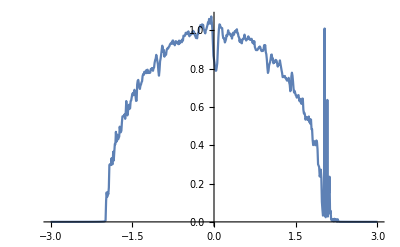

```mathematica
ListPlot[%160,Joined->True]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1],imp=imp[ω,δ,t,ϵ,ϵ1]},(*sl6=Inverse[IdentityMatrix[1]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[1]-imp.T.sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,q]; J=J];sl9=Inverse[IdentityMatrix[1]-imp.T.sl8.T].imp; sl10=Module[{J=sl9},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,r]; J=J];*)sl7=Module[{m=RandomInteger[{0,20}],n=RandomInteger[{0,20}],o=RandomInteger[{0,20}]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,m]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,n]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,o]; J=J]];tr:=Module[{},Il1:=Inverse[IdentityMatrix[1]-sl7.T1[1].SR[ω,0.001,1,0].T1[1]].sl7;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T1[1].sl7.T1[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];tr]
```

```mathematica
tr1[0,0.001,1,0,1]
```

0.520276

```mathematica
tr2[ω_,δ_,t_,ϵ_,ϵ1_,r_]:=Module[{J=SL[ω,δ,t,ϵ],A:=imp[ω,δ,t,ϵ,ϵ1],T:=t*IdentityMatrix[1],gg=g[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-A.T.Inverse[IdentityMatrix[1]-gg.T.J.T].gg.T].A,r]; J=J]
```

```mathematica
tr2[0,0.01,1,0,1,1]
```

{{0.-0.995012 ⅈ}}

```mathematica
Clear[tr2]
```

```mathematica
Mean[Table[sl6[0,0.001,1,0,1],10000]]
```

{{0.186925-0.684291 ⅈ}}

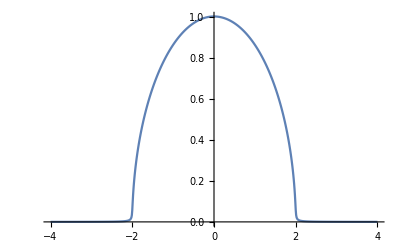

```mathematica
ListLinePlot[Table[{ω,-Im[SL[ω,0.001,1,0][[1,1]]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
B[ω_,n_,ϵ1_]:=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],B=imp[ω,0.001,1,0,ϵ1],T:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T.J.T].A,n]; J=J]
```

```mathematica
sl[ω_,δ_,t_,n_]:=Module[{x=RandomInteger[{0,1}],gg=imp[ω,0.001,1,0,1],T=t*IdentityMatrix[1],imp=imp[ω,0.001,1,0,1],η= SL[ω,0.001,1,0]},Do[η=Module[{},Inverse[IdentityMatrix[1]-imp.T.η.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,x]; J=J]],n];η=η]
```

```mathematica
Il1[ω_,δ_,t_,n_]:=Inverse[IdentityMatrix[1]-sl[ω,δ,t,n].T[t].SR[ω,δ,1,0].T[t]].sl[ω,δ,t,n]
```

```mathematica
Ir1[ω_,δ_,t_,n_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T[t].sl[ω,δ,t,n].T[t]].SR[ω,δ,1,0]
```

```mathematica
gdd1[ω_,δ_,t_,n_]:= Il1[ω,δ,t,n]-ConjugateTranspose[Il1[ω,δ,t,n]]
```

```mathematica
grr1[ω_,δ_,t_,n_]:= Ir1[ω,δ,t,n]-ConjugateTranspose[Ir1[ω,δ,t,n]]
```

```mathematica
Gnonlocal1[ω_,δ_,t_,n_]:= SR[ω,δ,1,0].T[t].Il1[ω,δ,t,n]
```

```mathematica
GNON1[ω_,δ_,t_,n_]:= Gnonlocal1[ω,δ,t,n]-ConjugateTranspose[Gnonlocal1[ω,δ,t,n]]
```

```mathematica
tr3[ω_,δ_,t_,n_]:=Abs[Tr[gdd1[ω,δ,t,n].T[t].grr1[ω,δ,t,n].T[t]-T[t].GNON1[ω,δ,t,n].T[t].GNON1[ω,δ,t,n]]]
```

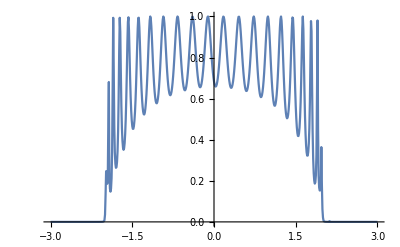

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.001,1,0,0.7]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
T[t_]:=t*IdentityMatrix[1]
```

```mathematica
sl[ω_,δ_,t_,n_]:=Module[{x=RandomInteger[{0,1}],gg=imp[ω,0.001,1,0,1],T=t*IdentityMatrix[1],imp=g[ω,0.001,1,0],η= SL[ω,0.001,1,0]},Do[η=Module[{},A:=Inverse[IdentityMatrix[1]-imp.T.η.T].imp;B:=Module[{J=A},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,x]]],n];η=η]
```

```mathematica
ll[ω_,δ_,t_,n_]:= Mean[Table[sl[ω,0.001,1,n],10000]]
```

```mathematica
Il1[ω_,δ_,t_,n_]:=Inverse[IdentityMatrix[1]-sl[ω,δ,t,n].T[t].SR[ω,δ,1,0].T[t]].sl[ω,δ,t,n]
```

```mathematica
Ir1[ω_,δ_,t_,n_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T[t].sl[ω,δ,t,n].T[t]].SR[ω,δ,1,0]
```

```mathematica
gdd1[ω_,δ_,t_,n_]:= Il1[ω,δ,t,n]-ConjugateTranspose[Il1[ω,δ,t,n]]
```

```mathematica
grr1[ω_,δ_,t_,n_]:= Ir1[ω,δ,t,n]-ConjugateTranspose[Ir1[ω,δ,t,n]]
```

```mathematica
Gnonlocal1[ω_,δ_,t_,n_]:= SR[ω,δ,1,0].T[t].Il1[ω,δ,t,n]
```

```mathematica
GNON1[ω_,δ_,t_,n_]:= Gnonlocal1[ω,δ,t,n]-ConjugateTranspose[Gnonlocal1[ω,δ,t,n]]
```

```mathematica
tr3[ω_,δ_,t_,n_]:=Abs[Tr[gdd1[ω,δ,t,n].T[t].grr1[ω,δ,t,n].T[t]-T[t].GNON1[ω,δ,t,n].T[t].GNON1[ω,δ,t,n]]]
```

```mathematica
Mean[Table[tr3[0.1,0.001,1,0],10000]]
```

0.989722

```mathematica
Mean[Table[sl[ω,0.001,1,10],10000]]
```

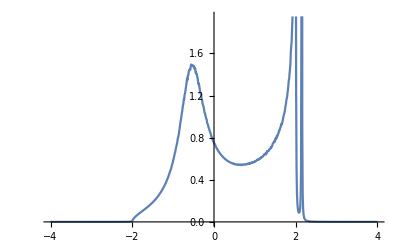

```mathematica
ListLinePlot[Table[{ω,Mean[Table[-Im[sl[ω,0.001,1,10][[1,1]]],10000]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
sl[ω_,δ_,t_,n_]:=Module[{x=RandomInteger[{0,1}],gg=imp[ω,0.001,1,0,1],T=t*IdentityMatrix[1],imp=g[ω,0.001,1,0],η= SL[ω,0.001,1,0]},Do[η=Module[{},A:=Inverse[IdentityMatrix[1]-imp.T.η.T].imp;B:=Module[{J=A},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,x]]],n]; η=η]
```

```mathematica
left[ω_,n_]:=Module[{η=SL[ω,0.001,1,0]},Do[η=Module[{gg=g[ω,0.001,1,0],T=1*IdentityMatrix[1]},Module[{J=Inverse[IdentityMatrix[1]-imp.T.η.T].imp},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,4]]],n];η=η]
```

```mathematica
left[0,10]
```

```mathematica
Do[η=Module[{gg=g[ω,0.001,1,0],T=1*IdentityMatrix[1]},Module[{J=Inverse[IdentityMatrix[1]-imp.T.η.T].imp},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,4]]],10]
```

```mathematica
T[t_]:=t*IdentityMatrix[1]
```

```mathematica
lleft[ω_,δ_,t_,ϵ_]:=Module[{x=RandomInteger[{1,50}]},Module[{J=SL[ω,δ,t,ϵ],A:=Inverse[β[ω,δ,1,1]],B:=Inverse[β[ω,δ,1,0]],T:=t*IdentityMatrix[1]},Do[J=Inverse[IdentityMatrix[1]-B.T.Inverse[IdentityMatrix[1]-A.T.J.T].A.T].B,x]; J=J]]
```

```mathematica
-Im[lleft[ω,0.001,1,0][[1,1]]]
```

$Aborted

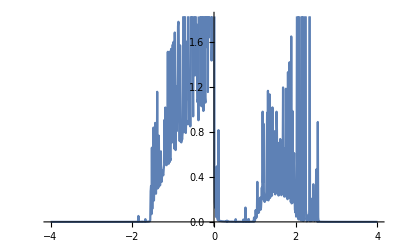

```mathematica
ListLinePlot[Table[{ω,-Im[lleft[ω,0.001,1,0][[1,1]]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Il1[ω_,δ_,t_,n_]:=Inverse[IdentityMatrix[1]-lleft[ω,δ,t,n].T[t].SR[ω,δ,1,0].T[t]].lleft[ω,δ,t,n]
```

```mathematica
Ir1[ω_,δ_,t_,n_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T[t].lleft[ω,δ,t,n].T[t]].SR[ω,δ,1,0]
```

```mathematica
gdd1[ω_,δ_,t_,n_]:= Il1[ω,δ,t,n]-ConjugateTranspose[Il1[ω,δ,t,n]]
```

```mathematica
grr1[ω_,δ_,t_,n_]:= Ir1[ω,δ,t,n]-ConjugateTranspose[Ir1[ω,δ,t,n]]
```

```mathematica
Gnonlocal1[ω_,δ_,t_,n_]:= SR[ω,δ,1,0].T[t].Il1[ω,δ,t,n]
```

```mathematica
GNON1[ω_,δ_,t_,n_]:= Gnonlocal1[ω,δ,t,n]-ConjugateTranspose[Gnonlocal1[ω,δ,t,n]]
```

```mathematica
tr3[ω_,δ_,t_,n_]:=Abs[Tr[gdd1[ω,δ,t,n].T[t].grr1[ω,δ,t,n].T[t]-T[t].GNON1[ω,δ,t,n].T[t].GNON1[ω,δ,t,n]]]
```

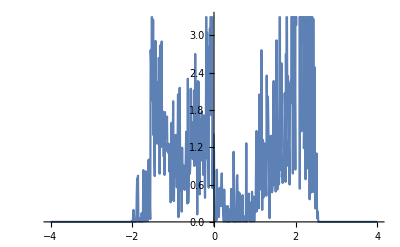

```mathematica
ListLinePlot[Table[{ω,tr3[ω,0.001,1,0]},{ω,Range[-4,4,0.01]}]]
```